# Signal and Noise

```mathematica
Needs["FourierSeries`"]
```

```mathematica
Clear["Global`*"]
```

## Sound

```mathematica
f=100;
```

```mathematica
sampleRate=8000;
```

```mathematica
time=3;
```

```mathematica
signal=Table[Sin[2π f t],{t,0,time,1/sampleRate}] ;
```

```mathematica
samples=Length[signal]
```

24001

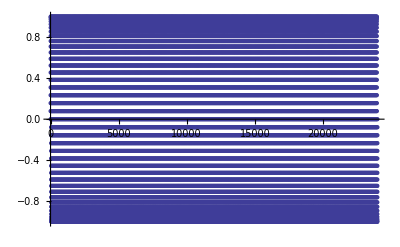

```mathematica
ListPlot[signal]
```

```mathematica
ListPlay[signal]
```

-Graphics-

## Noise

```mathematica
noise= 2RandomReal[0.1,{samples}];
```

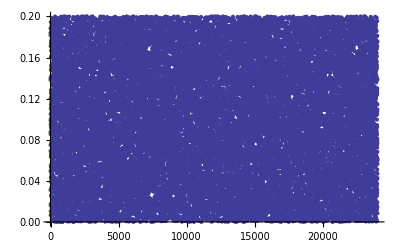

```mathematica
ListPlot[noise]
```

```mathematica
ListPlay[noise]
```

-Graphics-

## Signal and Noise

```mathematica
waveAndNoiseList=signal+noise ;
```

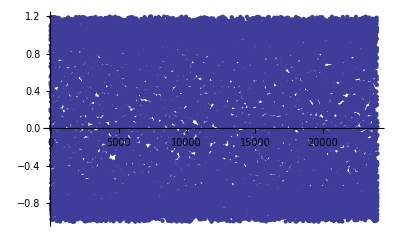

```mathematica
ListPlot[waveAndNoiseList]
```

```mathematica
ListPlay[waveAndNoiseList]
```

-Graphics-

## Export

### Get current notebook directory

```mathematica
CurrentNotebookDirectory=NotebookDirectory[SelectedNotebook[]]
```

/Users/Soha/Google Drive/Café Planck/1-Mathematics/21-Fourier analysis/07-FFT/

### Set Directory to current notebook directory

```mathematica
SetDirectory[CurrentNotebookDirectory]
```

/Users/Soha/Google Drive/Café Planck/1-Mathematics/21-Fourier analysis/07-FFT

### Get current notebook name

```mathematica
CurrentNotebookName=StringTake[ToString[SelectedNotebook[]],{18,StringPosition[ToString[SelectedNotebook[]],">",1][[1,1]]-1}]
```

Signal and Noise.nb

### Export

```mathematica
fileName=StringJoin[StringDrop[CurrentNotebookName,-3],".wav"];
```

```mathematica
Export[fileName,ListPlay[waveAndNoiseList]];
```